## Stan data analysis

### Full- and Half-Sibling models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/celtic_relationship_analysis

```mathematica
readStanDataset[filename_]:=Module[{rawD},
rawD=Import["model_siblings_output.csv"]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
ds=readStanDataset["model_siblings_output.csv"]
```

Dataset[<>]

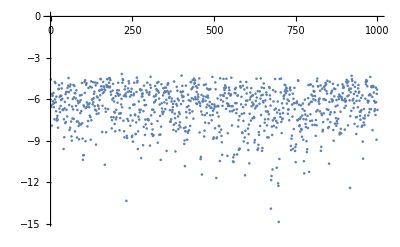

```mathematica
ListPlot[ds[[All,"lp__"]]]
```

Trajectory looks fine, no obvious burn-in or something.

```mathematica
ds[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
variableNames={"birth_date_mother","mother_age_hochdorf","mother_age_asperg","age_hochdorf","age_asperg","burial_date_hochdorf","burial_date_asperg"};
```

```mathematica
priorDistributions=AssociationThread[
variableNames,
{
UniformDistribution[{-600,-500}],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
NormalDistribution[-530,6],
NormalDistribution[-490,6]
}
]
```

<|birth_date_mother→UniformDistribution[{-600,-500}],mother_age_hochdorf→NormalDistribution[30,6],mother_age_asperg→NormalDistribution[30,6],age_hochdorf→NormalDistribution[45,6],age_asperg→NormalDistribution[30,6],burial_date_hochdorf→NormalDistribution[-530,6],burial_date_asperg→NormalDistribution[-490,6]|>

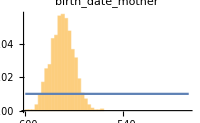
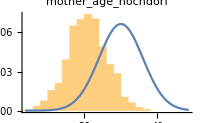
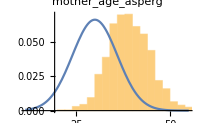
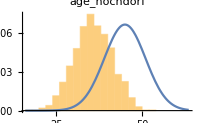
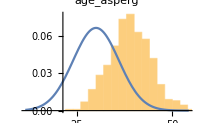
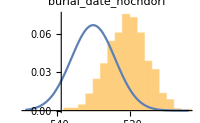
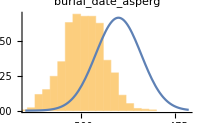

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
d=ds[All,v];
pd=priorDistributions[[v]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{v,variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[ds[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
birth_date_mother | -588.656 | -577.266 | -566.133
mother_age_hochdorf | 11.2697 | 20.7575 | 29.6282
mother_age_asperg | 30.7118 | 38.774 | 48.4151
age_hochdorf | 26.6839 | 35.6367 | 44.8355
age_asperg | 29.9564 | 38.981 | 47.6571
burial_date_hochdorf | -529.527 | -520.727 | -512.087
burial_date_asperg | -508.492 | -499.129 | -490.57

### Computing Marginal Likelihood

#### Naive prior sampling method

```mathematica
combinedPrior=ProductDistribution@@(Values[priorDistributions][[;;5]])
```

ProductDistribution[UniformDistribution[{-600,-500}],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[45,6],NormalDistribution[30,6]]

```mathematica
logLSiblings[paramVector_]:=Module[{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA,burialDateH,burialDateA},
{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA}=paramVector;
burialDateH=mothersBirthDate+birthAgeH+ageH;
burialDateA=mothersBirthDate+birthAgeA+ageA;
LogLikelihood[NormalDistribution[-530.,6],{burialDateH}]+
LogLikelihood[NormalDistribution[-490.,6],{burialDateA}]
]
```

```mathematica
unnormalisedLogPosteriorSiblings[paramVector_]:=LogLikelihood[combinedPrior,{paramVector}]+logLSiblings[paramVector]
```

```mathematica
priorSamples=RandomVariate[combinedPrior,100000];
```

```mathematica
loglValues=logLSiblings/@priorSamples;
```

```mathematica
Max[loglValues]
```

-5.68653

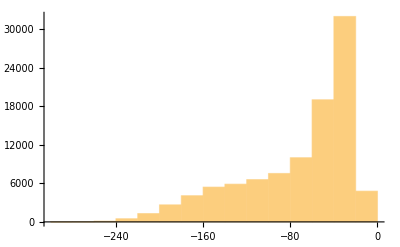

```mathematica
Histogram[loglValues]
```

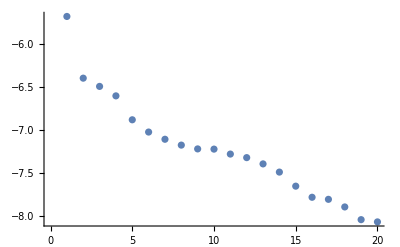

```mathematica
ListPlot[ReverseSort[loglValues][[;;20]]]
```

There are only very few points with a likelihood in the range of the maximum.

```mathematica
scalingFactor=Max[loglValues]
```

-5.68653

```mathematica
avgL=Log[Mean[Exp[loglValues-scalingFactor]]]+scalingFactor
```

-14.9862

We can assess the noise of this estimate by taking subsets:

```mathematica
avgL=Table[
Log[Mean[Exp[p-scalingFactor]]]+scalingFactor,
{p,Partition[loglValues,10000]}
]
```

{-15.1124,-15.429,-14.729,-14.7198,-15.6253,-15.2131,-14.5319,-14.4575,-16.1122,-15.0302}

But overall this is going to be biased, since the peak of the Likelihood distribution is not sufficiently covered by points. We can check this by asking how many points of the prior draws are within the high Likelihood region of the posterior:

```mathematica
posteriorDraws=Normal[ds[All,Values]][[All,8;;12]];
```

```mathematica
posteriorLogLvalues=unnormalisedLogPosteriorSiblings/@posteriorDraws;
```

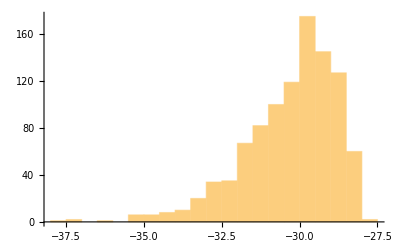

```mathematica
Histogram[posteriorLogLvalues]
```

```mathematica
ρ=Median[posteriorLogLvalues]
maxIndex=Ordering[posteriorLogLvalues,-1]//First;
θStar=posteriorDraws[[maxIndex]]
d=Covariance[posteriorDraws]
```

-29.9702

{-576.249,21.6535,39.1657,34.6265,38.4911}

{{47.9274,-14.0027,-16.7341,-17.4517,-14.6524},{-14.0027,28.5466,6.94773,-7.16135,2.79157},{-16.7341,6.94773,29.635,5.75356,-7.3986},{-17.4517,-7.16135,5.75356,29.8205,6.43217},{-14.6524,2.79157,-7.3986,6.43217,28.9924}}

The region of high likelihood is going to be within the radiuses of the ellipsoid defined by d:

```mathematica
√(Diagonal@d)
```

{6.92296,5.34291,5.44381,5.46082,5.38446}

The number of prior draws within the ellipsoid are:

```mathematica
Module[{invMat,r,insideNr},
TableForm[Table[
invMat=Inverse[d r^2];
insideNr=Length@Select[priorSamples,(#-θStar).invMat.(#-θStar)<1&];
{r,insideNr,Quantity[100.0insideNr/Length@priorSamples,"Percent"]},
{r,{1,2,3,4,5}}
],TableHeadings->{None,{"Z score", "Nr of draws","Ratio of draws"}}]]
```

Z score | Nr of draws | Ratio of draws
1 | 2 | 0.002 %
2 | 71 | 0.071 %
3 | 697 | 0.697 %
4 | 2742 | 2.742 %
5 | 7710 | 7.71 %

So we have less than 1% prior draws within Z<3 . Definitely not enough to compute marginal likelihood.

Let’s see how many posterior draws are within Z=3:

```mathematica
Module[{invMat,r,insideNr},
TableForm[Table[
invMat=Inverse[d r^2];
insideNr=Length@Select[posteriorDraws,(#-θStar).invMat.(#-θStar)<1&];
{r,insideNr,Quantity[100.0insideNr/Length@posteriorDraws,"Percent"]},
{r,{1,2,3,4,5}}
],TableHeadings->{None,{"Z score", "Nr of draws","Ratio of draws"}}]]
```

Z score | Nr of draws | Ratio of draws
1 | 28 | 2.8 %
2 | 442 | 44.2 %
3 | 887 | 88.7 %
4 | 995 | 99.5 %
5 | 1000 | 100. %

So 44% inside Z=3, much bigger fraction than with the prior draws.

#### Method by Reichl et al.

```mathematica
pointInVolumeA1Q[params_,ρ_]:=unnormalisedLogPosteriorSiblings[params]>ρ
```

```mathematica
pointInVolumeA2Q[params_,θStar_,mat_]:=Module[{v,i},
v=params-θStar;
i=Inverse[mat];
v.i.v<1
]
```

```mathematica
Length[Select[posteriorDraws,pointInVolumeA2Q[#,θStar,d 3^2]&]]
```

887

```mathematica
pointInVolumeAQ[params_,θStar_,mat_,ρ_]:=pointInVolumeA1Q[params,ρ]&&pointInVolumeA2Q[params,θStar,mat]
```

```mathematica
α=4.784;(*found by trial and error to yield 49%*)
Length[Select[posteriorDraws,pointInVolumeAQ[#,θStar,d α,ρ]&]]
```

490

OK, so within 2.095 times the standard ellipsoid we have 49% of posterior draws being inside, and yielding log likelihoods greater than the median.

Let’s see whether we can find the right α also automatically:

Using the function from Reichl 2020:

```mathematica
(*The following is from Reichl 2020 Appendix A.3*)
getAlpha[posteriorDraws_,unnormalisedLoglValues_,θStar_,d_]:=Module[{lP,l,ρ,lpHigh,logLValues,lpLow,αLow=0.01,αHigh=100.0,α,αMax,αMin,c,δA,zip},
l=Length@posteriorDraws;
ρ=Median[unnormalisedLoglValues];
lP=0.49l;
αMax=αHigh;
αMin=αLow;
δA=αHigh-αLow;
c=0;
While[δA>0.1,
δA=αHigh-αLow;
{lpLow,lpHigh}=Table[
zip=Transpose[{posteriorDraws,unnormalisedLoglValues}];
Length[Select[zip,pointInVolumeA2Q[#[[1]],θStar,α d]&&#[[2]]>ρ&]],
{α,{αLow,αHigh}}
];
If[lpHigh>lP,
If[c==0,αMax=Max[αHigh,αMax],If[αHigh<αMax,αMax=αHigh]];
αHigh=(αLow+αHigh)/2;
c=1;,
If[c==1,αHigh=Min[αHigh+10,αMax],αHigh=αHigh+100]
];
If[lpLow<lP,
If[αLow>αMin,αMin==αLow];
αLow=(αLow+αHigh)/2;,
αLow=Max[(1+αLow)/2,αMin];
]
];
αHigh
]
```

```mathematica
α=getAlpha[posteriorDraws,posteriorLogLvalues,θStar,d]
```

4.76855

```mathematica
√%
```

2.1837

Here is the function to draw uniformly from within an ellipsoid:

```mathematica
(*This is from Reichl et al 2020*)
getEllDraw[θStar_,mat_]:=Module[{k,rs,pt,λs,λh,eVals,eVecs},
k=Length@mat;
rs=RandomVariate[UniformDistribution[]];
pt=RandomVariate[NormalDistribution[],k];
λs=Total[pt^2];
λh=rs^(1/k)/√λs;
eVals=Eigenvalues[mat];
eVecs=Transpose@Eigenvectors[mat];
(λh pt eVals).eVecs+θStar
]
```

We show in the Appendix that this works indeed!

And here is the function to compute the log Volume of an ellipsoid:

```mathematica
(*This is from Reichl et al. 2020*)
getEllipsoidVolume[mat_]:=Module[{k=Length@mat,v,e,i},
v=Table[0,k+1];
e=Eigenvalues@mat;
v[[1]]=Log[1];
v[[2]]=Log[2];
For[i=3,i<=k+1,i++,v[[i]]=Log[(2Pi)/(i-1)]+v[[i-2]]];
v[[k+1]]+Total[Log@Sqrt[e]]
]
```

```mathematica
getEllipsoidVolume[DiagonalMatrix[{0.5,2}]]//Exp
```

3.14159

We continue to draw N points from the volume:

```mathematica
Diagonal[α d]//Sqrt
```

{15.1177,11.6673,11.8877,11.9248,11.758}

```mathematica
volumeDraws=Table[getEllDraw[θStar[[;;2]],α d[[;;2,;;2]]],1000];
```

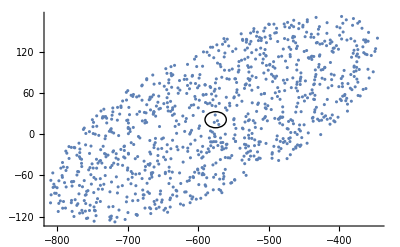

```mathematica
ListPlot[volumeDraws,Epilog->Circle[θStar[[;;2]],Sqrt[Diagonal[α d][[;;2]]]]]
```

and measure how many of them have likelihoods > ρ:

```mathematica
Length@Select[volumeDraws,unnormalisedLogPosteriorSiblings[#]>ρ&]
```

408

OK, so enough for a precise measurement. So we set π̂ according to Reichl 2020

```mathematica
piHat=N[Length@Select[volumeDraws,logLSiblings[#]>ρ&]/Length@volumeDraws]
```

0.1808

So our estimate of Volume A is then

```mathematica
vA=getEllipsoidVolume[α d]piHat
```

2.07768

We also need to compute the sum of inverse likelihoods as per equation 2.1 in Reichl 2020. Here we scale by the median to bring the likelihood more in range for computation

```mathematica
κScaled=Module[{logl,scaledLogL,scaledL,θ,κScaled},
Total@Table[
logl=logLSiblings[θ];
scaledLogL=logl-ρ;
scaledL=Exp[scaledLogL];
If[pointInVolumeAQ[θ,θStar,α d,ρ],1/scaledL,0],
{θ,posteriorDraws}
]]
κ=κScaled Exp[-ρ]
```

5.98803×10^-8

621108.

And the final result for the marginal likelihood (Log-Evidence) should be:

```mathematica
marginalLikelihood=vA/κ
```

3.34512×10^-6

which corresponds to a log-evidence of

```mathematica
Log[marginalLikelihood]
```

-12.608

## Appendix

#### Some visualisations of ellipsoid volumes

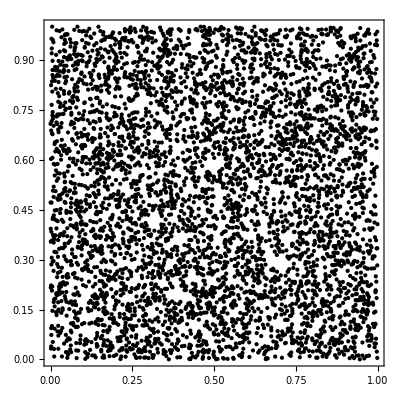

```mathematica
randomPoints=RandomVariate[UniformDistribution[10000]]//Partition[#,2]&;
colors=Table[If[pointInVolumeQ2Q[p,{0.5,0.5},DiagonalMatrix[{0.2,.4}^2]],Red,Blue],{p,randomPoints}];
Graphics[Point[randomPoints,VertexColors->colors],AspectRatio->1,ImagePadding->20,Frame->True]
```

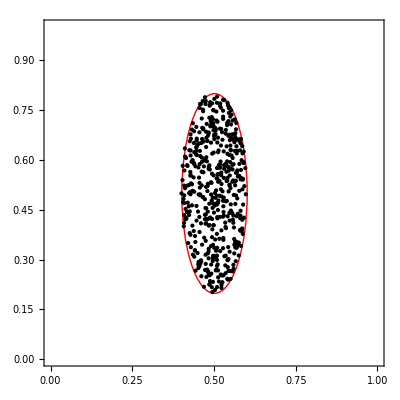
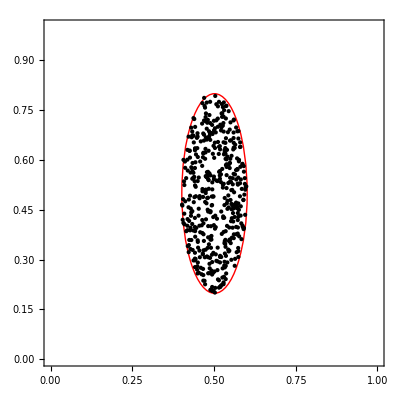

```mathematica
radii={.1,.3};
ellipsoidPoints=Table[getEllDraw[{0.5,0.5},DiagonalMatrix[radii]],500];
opts={Frame->True,AspectRatio->1,ImagePadding->20,ImageSize->400};
Row[{
Graphics[
{
Red,Circle[{0.5,0.5},radii],
Black,
Opacity[1],
Point[ellipsoidPoints]
},PlotRange->{{0,1},{0,1}},Sequence@@opts],
Graphics[
{
Red,Circle[{0.5,0.5},sqrtRadii],
Black,
Opacity[1],
Point[Select[randomPoints,pointInVolumeQ2Q[#,{0.5,0.5},DiagonalMatrix[radii^2]]&]]
},PlotRange->{{0,1},{0,1}},Sequence@@opts]
}]
```